```mathematica
-Graphics-


Clear["Global`*"];(*Clear all variables*)
```

```mathematica
T1 = 1/2*C12*(Φ0/(2*Pi))^2*(fd1-fd2)^2+1/2*C13*(Φ0/(2*Pi))^2*(fd1-fd3)^2+1/2*C23*(Φ0/(2*Pi))^2*(fd2-fd3)^2;
T2 = 1/2*C1g*(Φ0/(2*Pi))^2*(fd1)^2+1/2*C2g*(Φ0/(2*Pi))^2*(fd2)^2+1/2*C3g*(Φ0/(2*Pi))^2*(fd3)^2;
T3 = 1/2*C67*(Φ0/(2*Pi))^2*(fd6-fd7)^2+1/2*C78*(Φ0/(2*Pi))^2*(fd7-fd8)^2+1/2*C68*(Φ0/(2*Pi))^2*(fd6-fd8)^2;
T4 = 1/2*C6g*(Φ0/(2*Pi))^2*(fd6)^2+1/2*C7g*(Φ0/(2*Pi))^2*(fd7)^2+1/2*C8g*(Φ0/(2*Pi))^2*(fd8)^2;
T5 =  1/2*Ck*(Φ0/(2*Pi))^2*(fd3-fd8)^2;
T = T1+T2+T3+T4+T5;
U1 = 1/2*(Φ0/(2*Pi))^2*f2^2/Lg+1/2*(Φ0/(2*Pi))^2*f3^2/Lg+(I0*Φ0)/(4*Pi)*f1^2;
U2 =  1/2*(Φ0/(2*Pi))^2*f8^2/Lg+1/2*(Φ0/(2*Pi))^2*f7^2/Lg+(I0*Φ0)/(4*Pi)*f6^2;
U3 = 1/2*(Φ0/(2*Pi))^2*(f3-f8)^2/Lk;
U = U1+U2+U3;
```

```mathematica
L = T-U;
P1 = D[L,fd1];P2 = D[L,fd2];P3 = D[L,fd3];P6 = D[L,fd6];P7 = D[L,fd7];P8 = D[L,fd8];
R = {{Coefficient[P1,fd1,1],Coefficient[P1,fd2,1],Coefficient[P1,fd3,1],Coefficient[P1,fd6,1],Coefficient[P1,fd7,1],Coefficient[P1,fd8,1]},
{Coefficient[P2,fd1,1],Coefficient[P2,fd2,1],Coefficient[P2,fd3,1],Coefficient[P2,fd6,1],Coefficient[P2,fd7,1],Coefficient[P2,fd8,1]},
{Coefficient[P3,fd1,1],Coefficient[P3,fd2,1],Coefficient[P3,fd3,1],Coefficient[P3,fd6,1],Coefficient[P3,fd7,1],Coefficient[P3,fd8,1]},
{Coefficient[P6,fd1,1],Coefficient[P6,fd2,1],Coefficient[P6,fd3,1],Coefficient[P6,fd6,1],Coefficient[P6,fd7,1],Coefficient[P6,fd8,1]},
{Coefficient[P7,fd1,1],Coefficient[P7,fd2,1],Coefficient[P7,fd3,1],Coefficient[P7,fd6,1],Coefficient[P7,fd7,1],Coefficient[P7,fd8,1]},
{Coefficient[P8,fd1,1],Coefficient[P8,fd2,1],Coefficient[P8,fd3,1],Coefficient[P8,fd6,1],Coefficient[P8,fd7,1],Coefficient[P8,fd8,1]}
};
S = Inverse[R];
p  = {{p1},{p2},{p3},{p6},{p7},{p8}};
H =(1/2*Transpose[p].S.p+U)[[1,1]];
(***********************************************************************************************)
coeffp1 = Coefficient[H,p1,2];coefff1 = Coefficient[H,f1,2];
coeffp2 = Coefficient[H,p2,2];coefff2 = Coefficient[H,f2,2];
coeffp3 = Coefficient[H,p3,2];coefff3 = Coefficient[H,f3,2];
coeffp6 = Coefficient[H,p6,2];coefff6 = Coefficient[H,f6,2];
coeffp7 = Coefficient[H,p7,2];coefff7 = Coefficient[H,f7,2];
coeffp8 = Coefficient[H,p8,2];coefff8 = Coefficient[H,f8,2];
coeffp1p2 = Coefficient[H,p1*p2];coeffp1p3 = Coefficient[H,p1*p3];coeffp1p6 = Coefficient[H,p1*p6];coeffp1p7 = Coefficient[H,p1*p7];coeffp1p8 = Coefficient[H,p1*p8];
coeffp2p3 = Coefficient[H,p2*p3];coeffp2p6 = Coefficient[H,p2*p6];coeffp2p7 = Coefficient[H,p2*p7];coeffp2p8 = Coefficient[H,p2*p8];
coeffp3p6 = Coefficient[H,p3*p6];coeffp3p7 = Coefficient[H,p3*p7];coeffp3p8 = Coefficient[H,p3*p8];
coeffp6p7 = Coefficient[H,p6*p7];coeffp6p8 = Coefficient[H,p6*p8];
coeffp7p8 = Coefficient[H,p7*p8];
coefff3f8 = Coefficient[H,f3*f8];
r1 = 2*coefff1;b1 = 2*coeffp1;
r2 = 2*coefff2;b2 = 2*coeffp2;
r3 = 2*coefff3;b3 = 2*coeffp3;
r6 = 2*coefff6;b6 = 2*coeffp6;
r7 = 2*coefff7;b7 = 2*coeffp7;
r8 = 2*coefff8;b8 = 2*coeffp8;
ω1 = Sqrt[r1*b1];ω2 = Sqrt[r2*b2];ω3 = Sqrt[r3*b3];ω6 = Sqrt[r6*b6];
ω7 = Sqrt[r7*b7];ω8 = Sqrt[r8*b8];
(***********************************************************************************************)
```

```mathematica
(***********************************************************************************************)
Nlevel =4;
adiag = N[Table[Sqrt[i],{i,Nlevel-1}]];idiag =  N[Table[1,{i,Nlevel}]];
a = N[DiagonalMatrix[adiag,1]];
i = N[DiagonalMatrix[idiag]];
a1 = KroneckerProduct[a,i,i,i,i,i];a1d =ConjugateTranspose[a1];
a2 = KroneckerProduct[i,a,i,i,i,i];a2d = ConjugateTranspose[a2];
a3 = KroneckerProduct[i,i,a,i,i,i];a3d = ConjugateTranspose[a3];
a6 = KroneckerProduct[i,i,i,a,i,i];a6d = ConjugateTranspose[a6];
a7 = KroneckerProduct[i,i,i,i,a,i];a7d =ConjugateTranspose[a7];
a8 = KroneckerProduct[i,i,i,i,i,a];a8d = ConjugateTranspose[a8];
it = KroneckerProduct[i,i,i,i,i,i];
(***********************************************************************************************)
```

```mathematica
C12 = 28.1*10^-15;C13 = 28.1*10^-15;C23 = 6.3*10^-15;C1g =29.6*10^-15;C2g =58.0*10^-15;C3g = 58.0*10^-15;
C67 = 28.1*10^-15;C68 = 28.1*10^-15;C78 = 6.3*10^-15;C6g = 29.6*10^-15;C7g =58.0*10^-15;C8g = 58.0*10^-15;
Ck = 140.0*10^-15;
Lg = 0.450*10^-9;I0 = (280.0*10^-9*1000)/11500;Lc = 1.0*10^-9;
h = 6.62606896*10^-34;hbar = h/2.0/Pi;e = 1.60217662*10^-19;Φ0 = h/2/e;
Ikc = (280.0*10^-9*1000)/750;Lkc = Φ0/(2*Pi)*1/Ikc;
```

```mathematica
fn=Function[θ,
Block[{},

 Lk =Lkc/Cos[θ];
(*rule1 = {x_ y_ :>x.y,x_^2:>x.x};
rule2 = {(x_/;Element[x,Reals]).y_:>x*y};
H1 = Expand[H]//.rule1;
He = H1//.rule2;
He = coefff1*f1.f1+coefff2*f2.f2+coefff3*f3.f3+coefff6*f6.f6+coefff7*f7.f7+coefff8*f8.f8+coefff3f8*f3.f8+coeffp1*p1.p1+coeffp2*p2.p2+coeffp3*p3.p3+coeffp6*p6.p6+coeffp7*p7.p7+coeffp8*p8.p8+coeffp1p2*p1.p2+coeffp1p3*p1.p3+coeffp1p6*p1.p6+coeffp1p7*p1.p7+coeffp1p8*p1.p8+coeffp2p3*p2.p3+coeffp2p6*p2.p6+coeffp2p7*p2.p7+coeffp2p8*p2.p8+coeffp3p6*p3.p6+coeffp3p7*p3.p7+coeffp3p8*p3.p8+coeffp6p7*p6.p7+coeffp6p8*p6.p8+coeffp7p8*p7.p8;*)


f1 = Sqrt[hbar/2]*(b1/r1)^0.25*(a1+a1d);p1 =-I* Sqrt[hbar/2]*(r1/b1)^0.25*(a1-a1d);
f2 = Sqrt[hbar/2]*(b2/r2)^0.25*(a2+a2d);p2 =-I* Sqrt[hbar/2]*(r2/b2)^0.25*(a2-a2d);
f3 = Sqrt[hbar/2]*(b3/r3)^0.25*(a3+a3d);p3 =-I* Sqrt[hbar/2]*(r3/b3)^0.25*(a3-a3d);
f6 = Sqrt[hbar/2]*(b6/r6)^0.25*(a6+a6d);p6 =-I* Sqrt[hbar/2]*(r6/b6)^0.25*(a6-a6d);
f7 = Sqrt[hbar/2]*(b7/r7)^0.25*(a7+a7d);p7 =-I* Sqrt[hbar/2]*(r7/b7)^0.25*(a7-a7d);
f8 = Sqrt[hbar/2]*(b8/r8)^0.25*(a8+a8d);p8 =-I* Sqrt[hbar/2]*(r8/b8)^0.25*(a8-a8d);
He = hbar*ω1*(a1d.a1+it/2)+hbar*ω2*(a2d.a2+it/2)+hbar*ω3*(a3d.a3+it/2)+hbar*ω6*(a6d.a6+it/2)+hbar*ω7*(a7d.a7+it/2)+hbar*ω8*(a8d.a8+it/2)+coefff3f8*f3.f8+coeffp1p2*p1.p2+coeffp1p3*p1.p3+coeffp1p6*p1.p6+coeffp1p7*p1.p7+coeffp1p8*p1.p8+coeffp2p3*p2.p3+coeffp2p6*p2.p6+coeffp2p7*p2.p7+coeffp2p8*p2.p8+coeffp3p6*p3.p6+coeffp3p7*p3.p7+coeffp3p8*p3.p8+coeffp6p7*p6.p7+coeffp6p8*p6.p8+coeffp7p8*p7.p8;



result = Sort[Eigenvalues[He]/h/10^6][[1;;15]];
freq = (result[[2]]-result[[1]])/10^3;

g = (result[[3]]-result[[1]]-(result[[2]]-result[[1]]))/2;
output = {freq,g}
]];
```

```mathematica
Φlist = N[Table[-1.01+n*2.0/400.0,{n,0,400}]];
f[Φ_]:=(ϕ/.(NSolve[hbar/(2*e)*ϕ+N[Lc]*Ikc*Sin[ϕ] == -Φ*Φ0,ϕ,Reals]))[[1]];
ϕlist = N[Parallelize[ Map[f,Φlist]]];
```

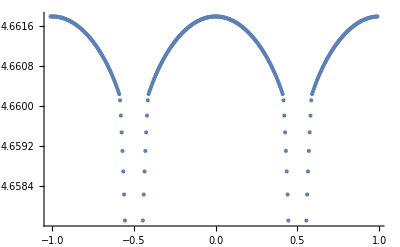

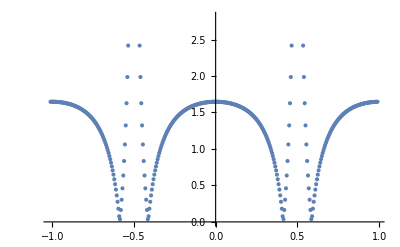

```mathematica
outputlist = Parallelize[ Map[fn,ϕlist]];
freqlist = outputlist[[;;,1]];
glist = outputlist[[;;,2]];

ListPlot[Table[{Φlist[[i]],freqlist[[i]]},{i,Length[Φlist]}]]
ListPlot[Table[{Φlist[[i]],glist[[i]]},{i,Length[Φlist]}]]
```

```mathematica
out = fn[0];
out-out[[1]]
```

{0.,5030.38,5062.91,10093.3,23921.,25250.3,26178.8,28920.8,29057.7,30310.3,30315.3,31178.9,31236.6,31851.9,34058.4}

```mathematica
out = fn[0];
out-out[[1]]
```

{0.,4694.41,4696.03,9390.2,9913.56,9913.84,14608.3,14609.2,18853.5,19827.2,23586.8,23623.1,23819.6,25666.3,28354.1}

```mathematica
out = fn[0];
out-out[[1]]
```

{0.,4661.79,4665.09,9326.62,9380.87,9381.02,14040.8,14047.5,14825.3,14825.3,17946.2,18761.4,19488.6,19488.7,22632.6}